# Fitting Weibull data

This notebook shows examples on how to fit data using the w-MLE estimator.

This Mathematica implementation is the first one, dating back from 2007.

Herein, the parameters are:
	α: the location parameter (aka the shift parameter)
	β: the spread parameter
	γ: the shape parameter

```mathematica
Quit[]
```

## Loading the library (adapt path to where you placed the “wMLE.m” file) and defining regular MLE method

```mathematica
Needs["wMLE`","C:\\Users\\DenisCousineau\\Desktop\\wMLE\\Mathematica\\wbl3wMLE.m"]
```

Package wMLE`
© Denis Cousineau (2007), denis.cousineau@uottawa.ca
This software is free of charge for academics and students
Use ? wMLE`* to see the list of functions available.

```mathematica
ll[data_,{γ_,β_,α_}]:=-∑_(i=1)^Length[data] Log[PDF[WeibullDistribution[γ,β,α],data⟦i⟧]]
MLE[data_]:=NMinimize[{ll[data,{pγ,pβ,pα}],pα≤ Min[data]&&pβ>0&& 0<pγ<10},
{{pα,Min[data]-0.1,Min[data]},{pβ,1,4},{pγ,1,2}},
Method->"NelderMead"
]
```

## Sample data set From K. Suzuki

```mathematica
suzuki={3.84,1.00,4.14,4.81,5.72,7.23,8.08,4.16,4.17,4.00,4.42,3.58,3.92,4.73,5.42,5.09,5.59,3.67,5.76,6.34,6.07,6.75,4.07,7.34,6.00,8.26,8.01,8.67,4.24,5.73,5.50};
Length[suzuki]
```

31

### Using regular MLE

```mathematica
{fitMLE,solMLE}=MLE[suzuki]
```

{60.0087,{pα→-0.784805,pβ→6.76832,pγ→4.06288}}

### Using wMLE

```mathematica
{fitwMLE,solwMLE}=wMLE[suzuki]
LogLikelihood[WeibullDistribution[γ,β,α]/.solwMLE,suzuki]
```

wMLE::badbnd: Bad starting value heuristics; use SetHeuristics.

{0,{γ→3.77234,β→6.49303,α→-0.522021}}

-60.0421

```mathematica
(*define pairs of starting values for shape and location*)
SetHeuristics[{1.3,2.3},{Min[suzuki]-1,Min[suzuki]}]
wMLE[suzuki]
LogLikelihood[WeibullDistribution[γ,β,α]/.%⟦2⟧,suzuki]
```

{0,{γ→3.77234,β→6.49303,α→-0.522021}}

-60.0421

### Showing a little plot

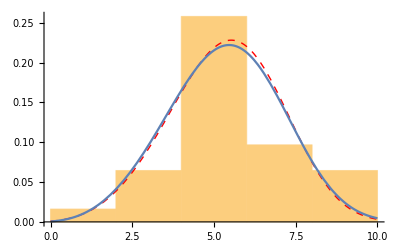

```mathematica
Show[{
Histogram[suzuki,Automatic,"PDF"],
Plot[PDF[WeibullDistribution[pγ,pβ,pα]/.solMLE,x],{x,0,10},PlotStyle->Directive[Dashed,Thick,Red]],
Plot[PDF[WeibullDistribution[γ,β,α]/.solwMLE,x],{x,0,10}]}]
```

## Rockette’s data

```mathematica
rockette={3.1,4.6,5.6,6.8};
Length[rockette]
```

4

```mathematica
{fitMLE,solMLE}=MLE[rockette]
```

NMinimize::nnum: The function value ∞ is not a number at {pα, pβ, pγ} = {3.1, 2.52749, 0.306102}.

{-3.61893,{pα→3.1,pβ→2.60533,pγ→0.29185}}

```mathematica
{fitwMLE,solwMLE}=wMLE[rockette]
```

{0.000133248,{γ→1.25955,β→2.70258,α→2.60857}}

```mathematica
SetHeuristics[{1.5,3.3},{0,0.1}]
{fitwMLE,solwMLE}=wMLE[rockette]
```

{0,{γ→2.48818,β→4.42024,α→1.07702}}

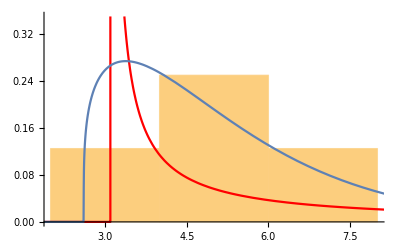

```mathematica
Show[{
Histogram[rockette,Automatic,"PDF"],
Plot[PDF[WeibullDistribution[pγ,pβ,pα]/.solMLE,x],{x,0,10},PlotStyle->Red,PlotRange->{0,0.35}],
Plot[PDF[WeibullDistribution[γ,β,α]/.solwMLE,x],{x,0,10}]}]
```

```mathematica
LogLikelihood[WeibullDistribution[pγ,pβ,pα]/.solMLE,{3.1,4.6,5.6,6.8}]
LogLikelihood[WeibullDistribution[γ,β,α]/.solwMLE,{3.1,4.6,5.6,6.8}]
```

3.61893

-7.10724

## Simulated data (takes roughly 10 minutes for 500)

Quick and dirty (and slow) Monte Carlo simulation for a single condition (n = 30, γ = 2).

It is typically better to use starting value heuristics that are much too small (more so for the shape). It avoids degenerate solutions (Cousineau, 2011).

Typically, MLE undershoots the shape parameter (here, it finds 1.90); wMLE should overestimate the shape parameter by half that magnitude (here, 2.05).

```mathematica
(res2=Table[
X=RandomVariate[WeibullDistribution[2,1,0],30];
{fitwMLE,solMLE}=MLE[X];
{pγ,pβ,pα}/.solMLE,
{500}
])//Mean[Select[#,#⟦1⟧<4.9&]]&//AbsoluteTiming
```

NMinimize::nnum: The function value ∞ is not a number at {pα, pβ, pγ} = {0.320064, 0.49011, 0.89856}.

NMinimize::nnum: The function value ∞ is not a number at {pα, pβ, pγ} = {0.519012, 0.406051, 0.87142}.

NMinimize::nnum: The function value ∞ is not a number at {pα, pβ, pγ} = {0.134398, 0.599617, 0.92233}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{767.7834,{1.89301,0.905803,0.0656126}}

```mathematica
(res=Table[
X=RandomVariate[WeibullDistribution[2,1,0],30];
(*roughly the lower bound of data*)
SetHeuristics[{0.25,2.75},{Min[X]-StandardDeviation[X]/2,Min[X]-0.001}];
{fitwMLE,solwMLE}=wMLE[X];
{γ,β,α}/.solwMLE,
{500}
])//Mean[Select[#,#⟦1⟧<4.9&]]&//AbsoluteTiming
```

wMLE::nosol: The solution found exceed 0.001; you may be in a region with no consistant solution (γ <^? 1).

General::stop: Further output of wMLE :: nosol will be suppressed during this calculation.

{561.4032,{1.99241,0.963042,0.0245456}}

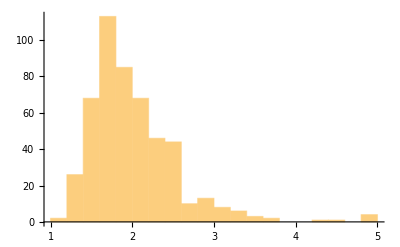

```mathematica
Histogram[res⟦All,1⟧]
```